```mathematica
nu=0.3;
volume=0.5;
thickBound=0.4;
smooth=0.6;
dMax=0.5;
countMax=100;
smoothN=100;
(*Cantilever*)
mn={m,n}={4,1}*40;
mn1={m1,n1}=mn+1;
fta[a_,b_]:=Flatten[Transpose@Array[a,b],1];
nodes=N[fta[{##}&,mn1]];
elems=fta[With[{k=#1+#2*m1},{k-m1,k-m,k+1,k}]&,mn];
fixXs=Range[1,m1*n1,m1];
fixYs=fixXs;
fixNs=(fixXs*2-1)~Union~(fixYs*2);
nodeForces={{m1*(n1+1)/2,{0,-1}}};
Remove[(*n,*)mn,m1,n1,mn1,fta,fixXs,fixYs];
nElems=Length[elems]
nNodes=Length[nodes]
```

6400

6601

```mathematica
numDel=nElems-Floor[nElems*volume+0.5]
```

3200

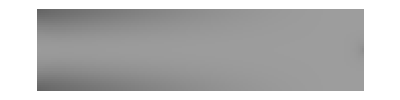
-Graphics- 1
0.0998383 h=0.14325

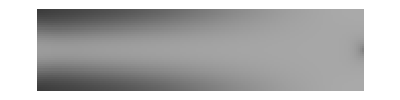
-Graphics- 2
0.241861 h=0.260005

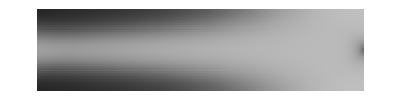
-Graphics- 3
0.399819 h=0.520009

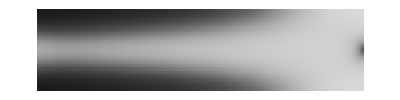
-Graphics- 4
0.568466 h=1.04002

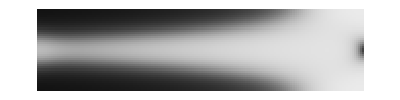
-Graphics- 5
0.735062 h=2.08004

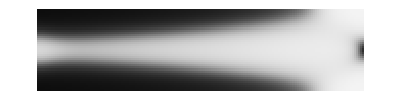
-Graphics- 6
0.871057 h=4.1028

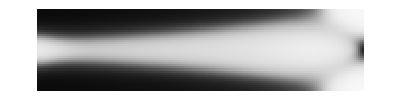
-Graphics- 7
0.931989 h=5.92415

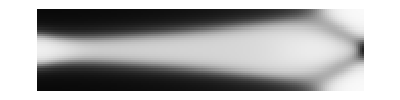
-Graphics- 8
0.944133 h=7.49854

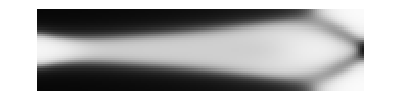
-Graphics- 9
1.00769 h=13.1465

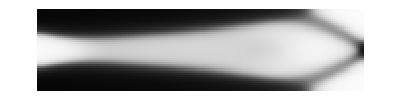
-Graphics- 10
1.11504 h=20.9171

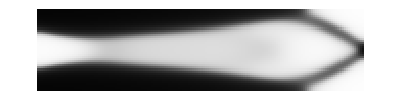
-Graphics- 11
1.20493 h=28.7723

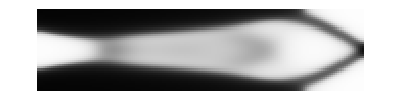
-Graphics- 12
1.23658 h=30.2028

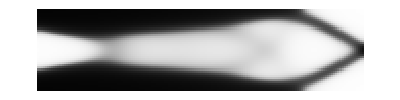
-Graphics- 13
1.2843 h=30.6244

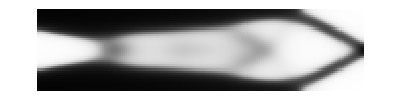
-Graphics- 14
1.29272 h=31.9249

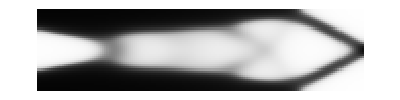
-Graphics- 15
1.33292 h=32.8224

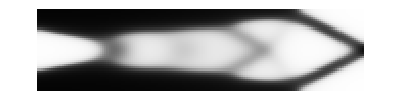
-Graphics- 16
1.32923 h=33.2806

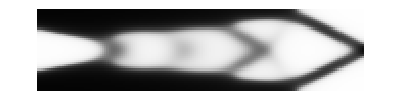
-Graphics- 17
1.39046 h=43.6107

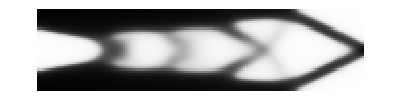
-Graphics- 18
1.43432 h=46.4179

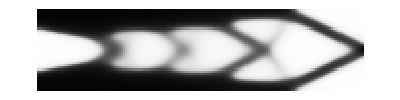
-Graphics- 19
1.47013 h=47.0659

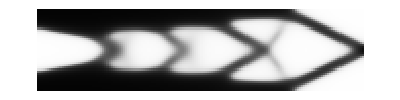
-Graphics- 20
1.50291 h=47.0659

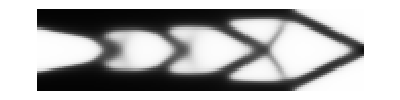
-Graphics- 21
1.53369 h=47.3932

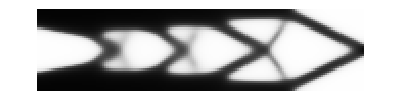
-Graphics- 22
1.58202 h=51.8621

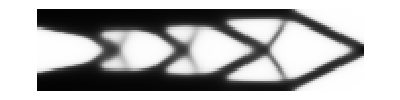
-Graphics- 23
1.646 h=65.1914

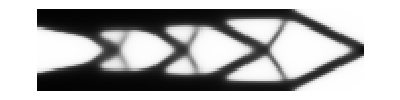
-Graphics- 24
1.66383 h=66.1014

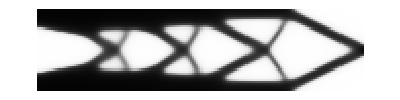
-Graphics- 25
1.70654 h=69.8704

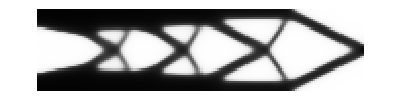
-Graphics- 26
1.78236 h=85.4263

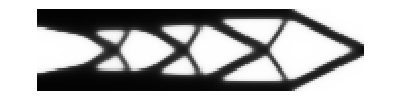
-Graphics- 27
1.88168 h=115.089

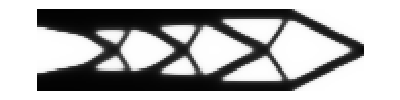
-Graphics- 28
1.99329 h=157.217

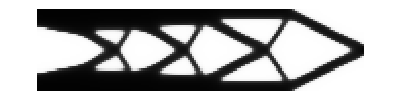
-Graphics- 29
2.11509 h=214.764

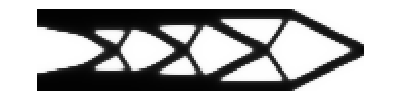
-Graphics- 30
2.18952 h=253.635

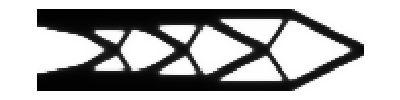
-Graphics- 31
2.26667 h=310.104

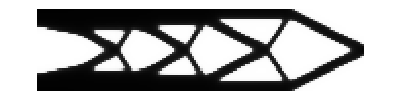
-Graphics- 32
2.33861 h=376.527

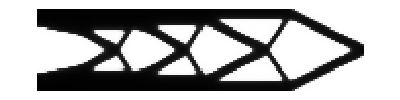
-Graphics- 33
2.38533 h=403.552

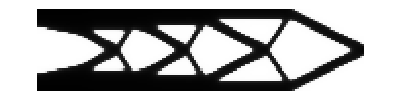
-Graphics- 34
2.42427 h=450.883

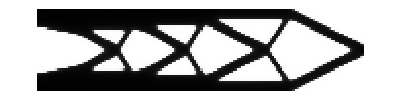
-Graphics- 35
2.46504 h=503.766

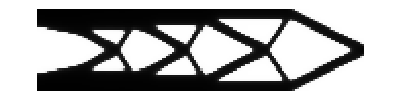
-Graphics- 36
2.49442 h=521.531

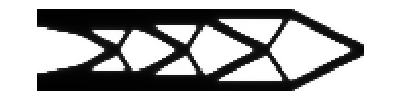
-Graphics- 37
2.50208 h=525.158

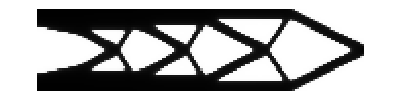
-Graphics- 38
2.53543 h=582.7

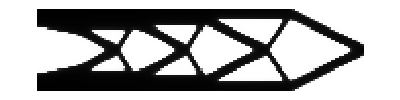
-Graphics- 39
2.60193 h=707.511

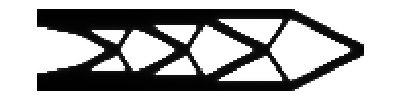
-Graphics- 40
2.68393 h=889.351

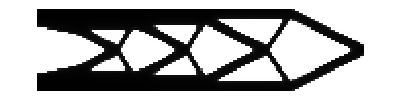
-Graphics- 41
2.78418 h=1206.5

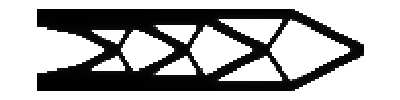
-Graphics- 42
2.92184 h=1671.13

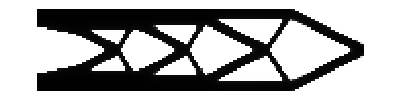
-Graphics- 43
2.92488 h=1682.75

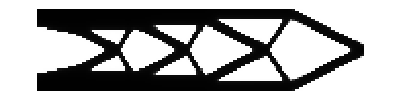
-Graphics- 44
2.9262 h=1682.75

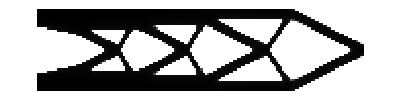
-Graphics- 45
2.9283 h=1682.75

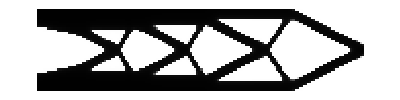
-Graphics- 46
2.93013 h=1682.75

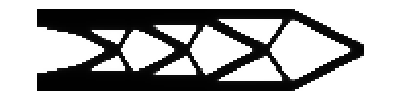
-Graphics- 47
2.93273 h=1682.75

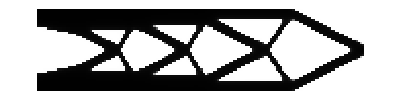
-Graphics- 48
2.9377 h=1706.24

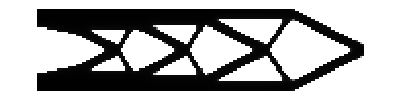
-Graphics- 49
2.98877 h=1959.96

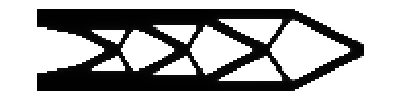
-Graphics- 50
2.9894 h=1959.96

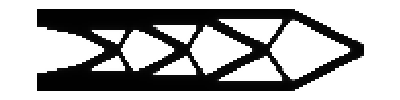
-Graphics- 51
2.98898 h=1959.96

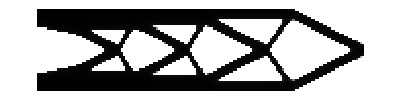
-Graphics- 52
2.98995 h=1959.96

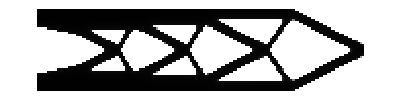
-Graphics- 53
2.99078 h=1959.96

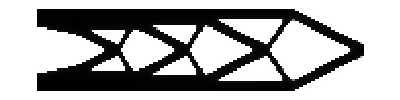
-Graphics- 54
2.9904 h=1959.96

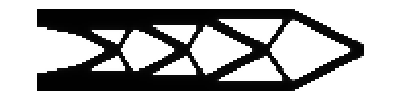
-Graphics- 55
2.99114 h=1959.96

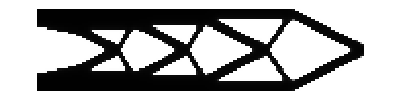
-Graphics- 56
2.99092 h=1959.96

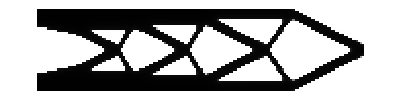
-Graphics- 57
2.99221 h=1959.96

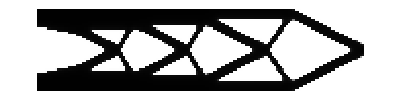
-Graphics- 58
2.99203 h=1959.96

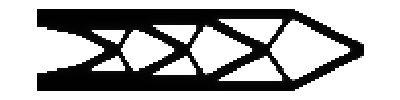
-Graphics- 59
2.99321 h=1959.96

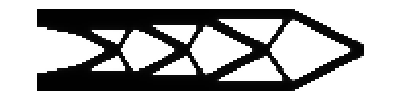
-Graphics- 60
2.99358 h=1959.96

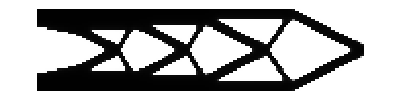
-Graphics- 61
2.9951 h=1959.96

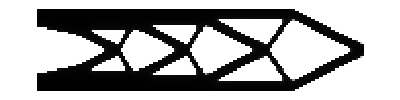
-Graphics- 62
2.99528 h=1959.96

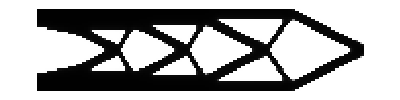
-Graphics- 63
2.99653 h=1959.96

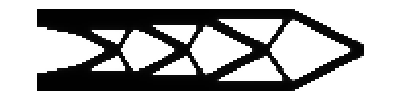
-Graphics- 64
2.99661 h=1959.96

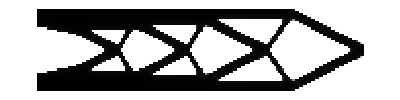
-Graphics- 65
2.99773 h=1959.96

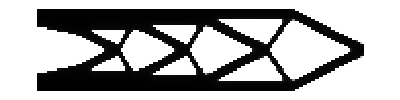
-Graphics- 66
2.99775 h=1959.96

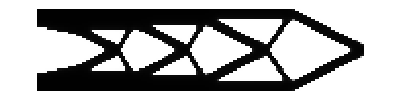
-Graphics- 67
2.99882 h=1959.96

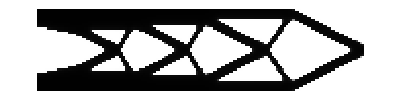
-Graphics- 68
2.99879 h=1959.96

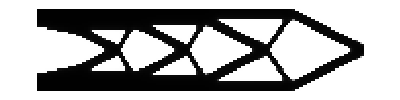
-Graphics- 69
2.9998 h=1959.96

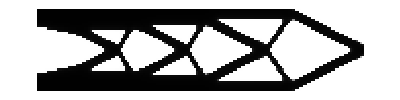
-Graphics- 70
2.99969 h=1959.96

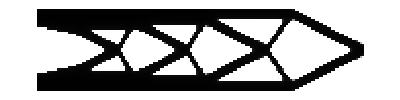
-Graphics- 71
3.00064 h=1959.96

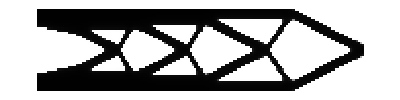
-Graphics- 72
3.00047 h=1959.96

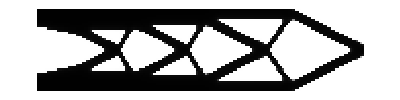
-Graphics- 73
3.00136 h=1959.96

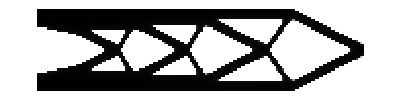
-Graphics- 74
3.00115 h=1959.96

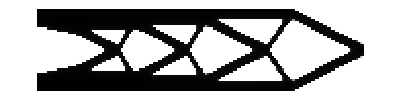
-Graphics- 75
3.00199 h=1959.96

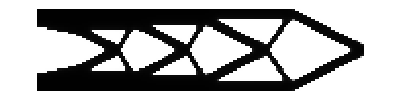
-Graphics- 76
3.00174 h=1959.96

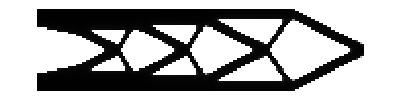
-Graphics- 77
3.00256 h=1959.96

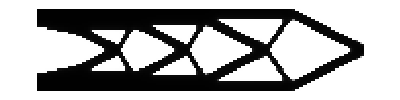
-Graphics- 78
3.00229 h=1959.96

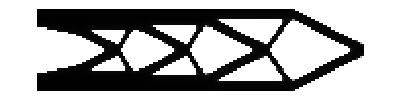
-Graphics- 79
3.0031 h=1959.96

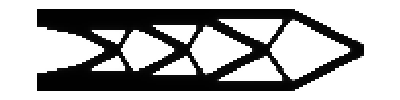
-Graphics- 80
3.00281 h=1959.96

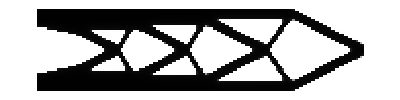
-Graphics- 81
3.00361 h=1959.96

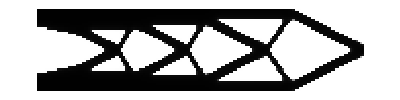
-Graphics- 82
3.0033 h=1959.96

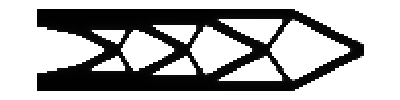
-Graphics- 83
3.00409 h=1959.96

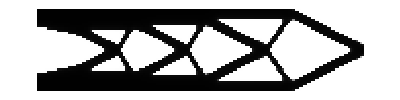
-Graphics- 84
3.00376 h=1959.96

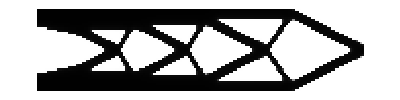
-Graphics- 85
3.00455 h=1959.96

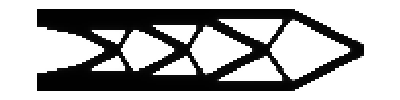
-Graphics- 86
3.0042 h=1959.96

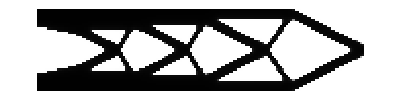
-Graphics- 87
3.00499 h=1959.96

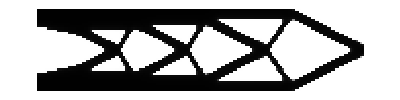
-Graphics- 88
3.00463 h=1959.96

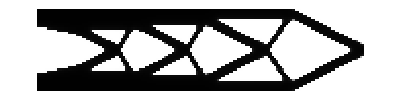
-Graphics- 89
3.00541 h=1959.96

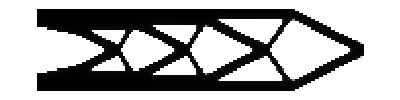
-Graphics- 90
3.00503 h=1959.96

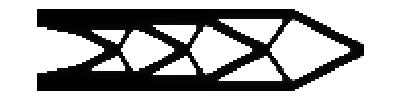
-Graphics- 91
3.0058 h=1959.96

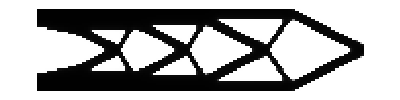
-Graphics- 92
3.00541 h=1959.96

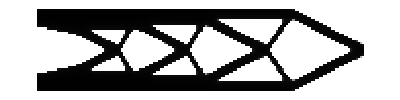
-Graphics- 93
3.00618 h=1959.96

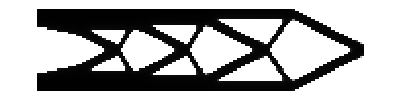
-Graphics- 94
3.00578 h=1959.96

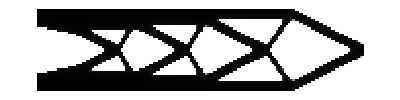
-Graphics- 95
3.00654 h=1959.96

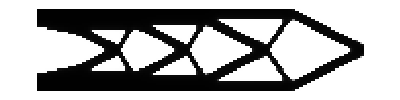
-Graphics- 96
3.00613 h=1959.96

-Graphics- 97
3.00689 h=1959.96

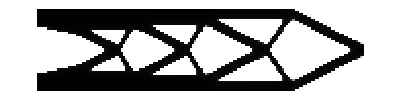
-Graphics- 98
3.00646 h=1959.96

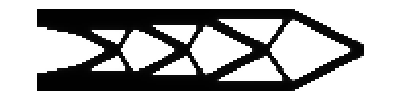
-Graphics- 99
3.00722 h=1959.96

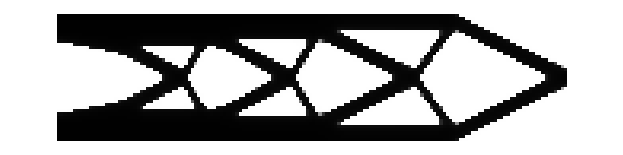
-Graphics- 100
3.00678 h=1959.96

```mathematica
filter=Flatten[GaussianFilter[Partition[#,m],{5*smooth,smooth},Padding->"Reversed"]]&;
elemK=Block[{k,m},k=({3,1,-3,-1,-3,-1,0,1}+{-1,1,-1,3,1,-1,1,-3}*nu)/({6,8,12,8,12,8,6,8}*(1-nu^2));
m={{2,3,4,5,6,7,8},{8,7,6,5,4,3},{6,7,4,5,2},{8,3,2,5},{2,3,4},{8,7},{6},{0}};
m=PadLeft[m,{8,8}];
m=IdentityMatrix[8]+m+Transpose[m];
k[[#]]&/@m];

energyFEM[{matIJ_,gather_,pos0_,f_,flatten3_},thicks_]:=Block[{matV,disp},matV=flatten3[Total/@Extract[Flatten[With[{p=Partition[elemK,{2,2}]},p*#&/@thicks],2],gather]];
matV[[pos0]]=0;
disp=Partition[LinearSolve[SparseArray[matIJ->matV],f,Method->Cholesky],2];
With[{d=Flatten[disp[[#]]]},Max[0.,d.elemK.d]]&/@elems];

prepare=Block[{matIJ,gather,nNodes,pos0,f,flatten3},matIJ=Flatten[Outer[List,#,#]&/@elems,2];
gather=SplitBy[Ordering[matIJ],matIJ[[#]]&];
gather=Block[{i},Replace[gather,{_,i_}->i,{2}]];
matIJ=matIJ[[gather[[All,1]]]];
gather=List/@gather;
nNodes=Max[elems];
matIJ=Flatten[Transpose[With[{p=Transpose[2*matIJ-1]},Transpose[p+#]&/@Tuples[{0,1},2]]],1];
Block[{fix=ConstantArray[False,2*nNodes]},fix[[fixNs]]=True;
pos0=Union@@(Flatten[Position[Extract[fix,List/@#],True,1]]&/@Transpose[matIJ]);
pos0=Extract[pos0,Position[Unequal@@@matIJ[[pos0]],True,1]];];
f=ConstantArray[{0,0},nNodes];
7 (f[[#[[1]]]]=#[[2]])&@Transpose[nodeForces];
f=Flatten[f];f[[fixNs]]=0;f=SparseArray[f];
flatten3=Compile[{{v,_Real,3}},Flatten[v]];
{matIJ,gather,pos0,f,flatten3}];

yFun=Compile[{{x,_Real,1}},(1.+Tanh[x])/2.];
xFun=Compile[{{y,_Real,1}},ArcTanh[2.y-1.]];

xBound=xFun[{thickBound}][[1]];
funBound=Mean[Sort[#][[{numDel,numDel+1}]]]-xBound&;
Block[{dMax1=dMax/smoothN,rh=2.^(1/smoothN),thicks=ConstantArray[thickBound,nElems],x=ConstantArray[xBound,nElems],energyPrev=ConstantArray[0.,nElems]},Block[{lam,dlam,h,energy},Do[energy=energyFEM[prepare,Max[10.^-7,#]&/@thicks]*thicks;
energy=filter[energy];
energy=0.5(energyPrev+energy);
energyPrev=energy;
If[count==1,lam=-Sort[energy][[numDel+1]];
dlam=0.001lam;
h=dMax/(smoothN*Mean[energy]);];
Block[{d=0.,u=x,u0,u1,dFilter,dDer,dAll,w,f1,f2},
Do[u0=u;
u=filter[u];
dFilter=Max[Abs[u-u0]];
u0=u;
w=h With[{y=yFun[u]},y*(1.-y)^2];
u+=w energy;
Do[f1=funBound[u+w (lam-dlam)];
f2=funBound[u+w (lam+dlam)];
If[Abs[f1+f2]<1000000.Abs[f1-f2],lam+=(f1+f2)/(f1-f2)dlam;];
u1=u+w lam;
If[Abs[funBound[u1]]<thickBound*0.001,Break[];];,{j,100}
];
u=u1;
dAll=Max[Abs[u-x]];
If[dMax<dAll,Break[];];
dDer=Max[Abs[u-u0]];
d+=dMax1;
If[dAll<d/rh||dDer<dFilter,h*=rh;];,{smoothN}
];
x=u;];
thicks=yFun[x];
Print[Graphics[Raster[Partition[1.-thicks,m]]]," ",count,"
",Sqrt[Mean[(x-xBound)^2]]," h=",h];,{count,countMax}];];];
```